# Cluster

## 聚类的目的

将数据划分为若干个簇，簇内相似性大，簇间相似性小，聚类效果好。用于从数据中提取信息和规律。

## K-Means

以下函数包括与中心集的距离函数distance和KMeans函数, KMeans函数输入数据x和要分类的个数k, 要求x中元素的个数不低于k值.

算法特点

#### 不一定得到全局最优解，当初始簇中心不满足要求时，可能只能得到局部最优解，当然有学者通过一定的预处理使得得到的初始簇中心满足一定条件，从而能够得到全局最优解，并将方法名改为k-means++

#### 不能排除噪声点对聚类的影响

#### 要求簇形状接近圆形

#### 要求完全聚类的情况

### 根据聚类中的均值进行聚类划分的k-means算法 输入: 聚类个数k, 以及包含n个数据对象的数据库. 输出: 满足方差最小标准的k个聚类

#### (1) 从n个数据对象任意选择k个对象作为初始聚类中心 (2) 循环(3)(4)直到每个聚类不再发生变化为止 (3) 根据每个聚类对象的均值(中心对象),计算每个对象与这些中心对象的距离; 并根据最小距离重新对相应对象进行划分; (4) 重新计算每个(有变化)聚类的均值(中心对象)

```mathematica
distance[x_,center__]:=Norm[x-#]&/@center;(*点与中心簇的距离*)
dist[x__,center_]:=Norm[#-center]&/@x;(*中心与点簇的距离*)
getMin[res__]:=First@Flatten@Position[res,Min[res]];
KMeans[x__,k_]:=Module[{center={},group={},flag=True,newcenter={}},
center=RandomSample[x,k];
While[flag,
group=Table[{},{i,k}];
(*样本和中心的距离计算, 并归并到最小距离分组*)
AppendTo[group[[getMin@distance[#,center]]],#]&/@x;
newcenter=Mean[#]&/@group;
If[newcenter==center,flag=False,center=newcenter]
];
{group,center,Total@Flatten[dist[group[[#]],center[[#]]]&/@Range[k]]}
(*TODO*)
]
```

43.0355

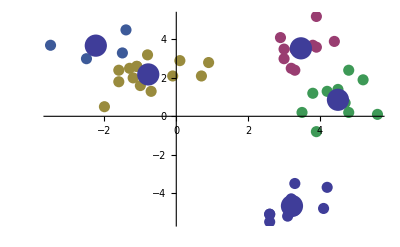

```mathematica
lst={{-1.1,2.6},{3.9,-0.8},{4.2,-3.7},{3.3,3.5},{3.9,5.2},{4.1,-4.8},{3.8,3.7},{5.6,0.1},{3.1,-5.2},{-0.9,2.3},{2.9,4.1},{-2.3,3.9},{-2.5,3.},{2.6,-5.5},{5.2,1.9},{-0.7,1.3},{0.9,2.8},{-1.5,3.3},{3.8,1.2},{2.6,-5.1},{-0.8,3.2},{4.7,0.7},{3.,3.},{3.9,3.6},{4.5,1.4},{4.2,1.3},{-1.1,2.6},{4.8,2.4},{3.3,-3.5},{3.2,-4.6},{3.3,-4.9},{3.,3.5},{0.7,2.1},{3.2,-4.3},{-2.,0.5},{-1.2,2.},{-1.6,1.8},{-3.5,3.7},{4.8,0.2},{3.3,2.4},{-0.1,2.1},{-1.3,2.5},{4.4,3.9},{3.5,0.2},{0.1,2.9},{-1.,1.6},{-1.4,4.5},{3.2,2.5},{-1.6,2.4},{2.6,-5.1}};
res=KMeans[lst,5];
res[[3]]
Show[{ListPlot[res[[1]],PlotRange->Full,PlotStyle->PointSize[0.02]],ListPlot[res[[2]],PlotRange->Full,PlotStyle->PointSize[0.04]]}]
```

### TODO 不同聚类结果的凝聚度度量

## FindClusters 内置函数

## 层次聚类算法 deprecated

## DBScan算法(Density-Based Spatial Clustering of Applications with Noise)

算法目的在于过滤低密度区域, 发现稠密度样本点, 可以发现任意形状的聚类簇. 与KMeans相比, 不必输入要划分的聚类个数. 聚类簇的形状没有bias. 可以在需要时输入过滤噪声的参数.

E领域: 给定对象半径为E内的区域称为该对象的E领域
核心对象: 如果给定对象E领域内的样本数不小于Minpts, 则称该对象为核心对象
直接密度可达: 对于样本集D, 如果样本点q在p的E领域内, 且p为核心对象, 则对象q从对象p直接密度可达.
密度可达: 对于样本集D, 给定一串样本点p1, p2, ..., pn, p=p1, q=pn, 假如对象pi从pi-1直接密度可达, 则对象q从对象p密度可达.
密度相连: 对于样本集合D中的任意一点O, 如果存在对象p到对象o密度可达, 并且对象q到对象o密度可达, 那么对象q到对象p密度相连.

DBScan目的是找到密度相连对象的最大集合.

### 输入: E--半径, MinPts--给定点在E领域内成为核心对象的最小领域点数, D--集合 输出: 目标类簇集合 repeat 判断输入点是否为核心对象 找出核心对象的E领域中的所有直接密度可达点 until 所有输入点都判断完毕 repeat 针对所有核心对象的E领域所有直接密度可达点找到最大密度相连对象集合,中间 涉及到一些密度可达对象的合并 until 所有核心对象的E领域都遍历完毕

## 针对呈线状数据原型的模糊C线(FCL)算法

## 针对超平面状的模糊C面(FCP)算法

## 模糊C壳(FCS)算法

## 模糊C聚类FCM